# Blatt 5 - Optimierung der Emittanz im DBA-Lattice

Jonas Neundorf & Jan Skottke

Definiere Konstanten

```mathematica
constants={c-> 3.*10^8, q-> 1.602*10^-19,m-> 0.511*10^-3,r0-> 2.818*10^-15,cq-> 3.8*10^-13};
```

Du kannst η mit “Esc h Esc” schreiben (dann musst du nicht immer “Esc et Esc” benutzten)
Und das geschwungene ℋ kannst du mit “Esc scH Esc” machen.

## Vorbereitungen

#### Berechnung der Dispersionfunktion

Definiere die Matritzen für die Magnete:

```mathematica
mF[f_]:={{1,0,0},{-1/f,1,0},{0,0,1}} (*fokussierender Quad*)
```

```mathematica
mD[s_, ρ_] := {{Cos[s/ρ], ρ*Sin[s/ρ], ρ*(1 - Cos[s/ρ])}, {-1/ρ*Sin[s/ρ], Cos[s/ρ], Sin[s/ρ]}, {0, 0, 1}}(*Dipol*)
```

Definiere Dispersionsfunktionen:

```mathematica
η[s_]:=ρ*(1-Cos[s/ρ])
```

```mathematica
dη[s_]=D[η[s],s];
```

Die Dispersion soll nach durchqueren des DBA sich nicht geändert haben. Aus dieser Bedingung lässt sich die Brennweite bestimmen.

```mathematica
eq={0,0,1}==mD[L,ρ].mF[f].mD[L,ρ].{η[0],dη[0],1}//FullSimplify (*Dispersion nach dem ersten Dipol*)
```

{0,0,1}=={(ρ (-2 f cos((2 L)/ρ)+2 f-2 ρ sin(L/ρ)+ρ sin((2 L)/ρ)))/(2 f),(cos(L/ρ) (2 f sin(L/ρ)+ρ (cos(L/ρ)-1)))/f,1}

```mathematica
focus=Solve[eq,f]//Flatten
```

{f→1/2 ρ tan(L/(2 ρ))}

Diese Brennweite muss der Quadropol haben, damit die Dispersion am Ende wieder bei {0,0,1} ist.

#### Tests

Definieren wir zunächst einige Parameter, die wir für den Test benötigen.

```mathematica
params = {L->5, ρ->600}
```

{L→5,ρ→600}

Die berechnete Brennweite liefert das gewünschte Ergebnis, dass die Dispersion nach dem 2. Dipol wieder bei {0,0,1} ist.

```mathematica
mD[L,ρ].mF[f].mD[L,ρ].{η[0],dη[0],1}//.focus//FullSimplify
```

{0,0,1}

Dispersion nach dem ersten Dipol:

```mathematica
dispd1=mD[L,ρ].{η[0],dη[0],1}//FullSimplify
```

{ρ-ρ cos(L/ρ),sin(L/ρ),1}

Dispersion nach dem Quadropol und dem zweiten Dipol: (Hier gehen wir nur davon aus, dass der Startpunkt im Quadropol liegt und NICHT im 1. Dipol, da die Dispersion nach dem Quadropol und 2. Dipol ja {η,-dη} sein sollte. Und das ist sie!! :))

```mathematica
dispqd2=mF[f].mD[L,ρ].{η[0],dη[0],1}//.focus//FullSimplify
```

{ρ-ρ cos(L/ρ),-sin(L/ρ),1}

Definieren wir nun die Dispersion innerhalb des gesamten DBA.

```mathematica
dispersion[s_]:= Piecewise[ {{mD[s,ρ], s < L},{mD[s-L, ρ].mF[f].mD[L, ρ], L < s≤ 2*L}}].{0, 0, 1}
```

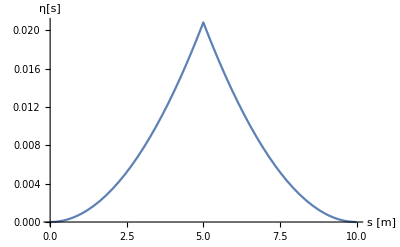

```mathematica
Plot[(dispersion[s] //.focus //.params)[[1]], {s, 0, 10}, AxesLabel->{"s [m]", "η[s]"}] (*Die Runden klammern sind wichtig, damit erst vom resultierenden Vektor das 1. Element genommen wird*)
```

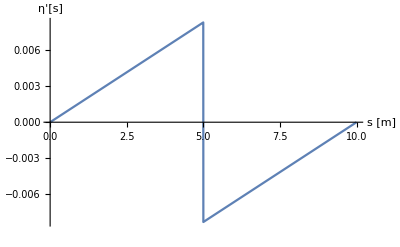

```mathematica
Plot[(dispersion[s] //.focus //.params)[[2]], {s, 0, 10}, AxesLabel-> {"s [m]", "η'[s]"}]
```

Hier wird dη geplottet:

```mathematica
fulldη[s_]=Piecewise[{{dispersion[s][[2,2]], s ≤ L}, {dispersion[s-L][[3,2]], L≤ s≤2*L}}]
```

Part::partw: Part 3 of (Piecewise[{{(cos(Times[«2»]) | ρ sin(«1») | ρ Plus[«2»]
-Power[«2»] sin(«1») | cos(Times[«2»]) | sin(Times[«2»])
0 | 0 | 1), -L+s<L}, {(Times[«3»]+Times[«2»] | Times[«3»]+Times[«3»] | Times[«2»]+Times[«3»]+Times[«3»]
Times[«4»]+Times[«2»] | Times[«2»]+Times[«3»] | Times[«2»]+sin(«1»)+Times[«3»]
0 | 0 | 1), L<-L+s≤2 L}}]).{0,0,1} does not exist.

Piecewise[{{0, s≤L}, {((Piecewise[{{(cos((s-L)/ρ) | ρ sin((s-L)/ρ) | ρ (1-cos((s-L)/ρ))
-(sin((s-L)/ρ))/ρ | cos((s-L)/ρ) | sin((s-L)/ρ)
0 | 0 | 1), s-L<L}, {(cos(L/ρ) (cos((s-2 L)/ρ)-(ρ sin((s-2 L)/ρ))/f)-sin(L/ρ) sin((s-2 L)/ρ) | ρ cos(L/ρ) sin((s-2 L)/ρ)+ρ sin(L/ρ) (cos((s-2 L)/ρ)-(ρ sin((s-2 L)/ρ))/f) | ρ (1-cos((s-2 L)/ρ))+ρ sin(L/ρ) sin((s-2 L)/ρ)+ρ (1-cos(L/ρ)) (cos((s-2 L)/ρ)-(ρ sin((s-2 L)/ρ))/f)
cos(L/ρ) (-(cos((s-2 L)/ρ))/f-(sin((s-2 L)/ρ))/ρ)-(cos((s-2 L)/ρ) sin(L/ρ))/ρ | cos(L/ρ) cos((s-2 L)/ρ)+ρ sin(L/ρ) (-(cos((s-2 L)/ρ))/f-(sin((s-2 L)/ρ))/ρ) | cos((s-2 L)/ρ) sin(L/ρ)+sin((s-2 L)/ρ)+ρ (1-cos(L/ρ)) (-(cos((s-2 L)/ρ))/f-(sin((s-2 L)/ρ))/ρ)
0 | 0 | 1), L<s-L≤2 L}}]).{0,0,1})⟦3,2⟧, L≤s≤2 L}}]

Part::partw: Part 3 of (Piecewise[{{(cos(Times[«2»]) | ρ sin(«1») | ρ Plus[«2»]
-Power[«2»] sin(«1») | cos(Times[«2»]) | sin(Times[«2»])
0 | 0 | 1), 0.000204286-L<L}, {(Times[«2»]+Times[«3»] | Times[«3»]+Times[«3»] | Times[«2»]+Times[«3»]+Times[«3»]
Times[«2»]+Times[«4»] | Times[«2»]+Times[«3»] | sin(«1»)+Times[«3»]+Times[«2»]
0 | 0 | 1), L<0.000204286-L≤2 L}}]).{0,0,1} does not exist.

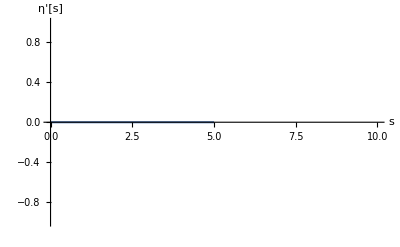

```mathematica
Plot[fulldη[x]//.focus//.{L ->5, ρ-> 10000}, {x, 0, 10}, AxesLabel-> {"s", "η'[s]"}]
```

#### Berechnung der Twiss Parameter (β-Funktionen)

```mathematica
bmat={{β0,-α0},{-α0,γ0}}
```

(β0 | -α0
-α0 | γ0)

```mathematica
drift[s_]:={{1,s},{0,1}}
```

```mathematica
quad[f_]:={{1,0},{-1/f,1}}
```

Zuerst berechnen wir die Parameter für den ersten Dipol:

```mathematica
twissd1[s_]=drift[s].bmat.Transpose[drift[s]]//FullSimplify
```

(γ0 s^2-2 α0 s+β0 | s γ0-α0
s γ0-α0 | γ0)

Nun zur Berechnung der Twissparameter für den letzten Teil, also für den Quadropol und dem zweiten Dipol: (Kommentar: Wenn ich mich richtig erinnere dann müsste folgendes gelten: B_1 = M * B_0 * M^T(das steht so im Skript) und weiter sollte gelten (das habe ich nicht im Skript gefunden): 
B_2 = M * B_1 * M^T= M * (M * B_0 * M^T) * M^T; wenn das nicht richtig ist, musst du ab hier einiges korrigieren :( )

```mathematica
twissqd2[s_]=drift[s].(quad[f].bmat.Transpose[quad[f]]).Transpose[drift[s]]//.focus//FullSimplify
```

(γ0 s^2-2 α0 s+(4 cot(L/(2 ρ)) (s α0 ρ-β0 ρ+s β0 cot(L/(2 ρ))) s)/ρ^2+β0 | -α0+s γ0+(2 cot(L/(2 ρ)) (2 s α0 ρ-β0 ρ+2 s β0 cot(L/(2 ρ))))/ρ^2
-α0+s γ0+(2 cot(L/(2 ρ)) (2 s α0 ρ-β0 ρ+2 s β0 cot(L/(2 ρ))))/ρ^2 | γ0+(4 cot(L/(2 ρ)) (α0 ρ+β0 cot(L/(2 ρ))))/ρ^2)

```mathematica
β[s_]=Piecewise[{{twissd1[s][[1,1]], s≤ L}, {twissqd2[s-L][[1,1]], L≤ s≤2*L}}]
```

Piecewise[{{β0+γ0 s^2-2 α0 s, s≤L}, {β0+(4 (s-L) cot(L/(2 ρ)) (-β0 ρ+α0 ρ (s-L)+β0 (s-L) cot(L/(2 ρ))))/ρ^2-2 α0 (s-L)+γ0 (s-L)^2, L≤s≤2 L}}]

```mathematica
α[s_]=Piecewise[{{-twissd1[s][[1,2]], s≤ L}, {-twissqd2[s-L][[1,2]], L≤ s≤2*L}}]
```

Piecewise[{{α0-γ0 s, s≤L}, {α0-(2 cot(L/(2 ρ)) (-β0 ρ+2 α0 ρ (s-L)+2 β0 (s-L) cot(L/(2 ρ))))/ρ^2-γ0 (s-L), L≤s≤2 L}}]

```mathematica
γ[s_]=Piecewise[{{twissd1[s][[2,2]], s<=L}, {twissqd2[s-L][[2,2]], L≤ s≤2*L}}]
```

Piecewise[{{γ0, s≤L}, {γ0+(4 cot(L/(2 ρ)) (α0 ρ+β0 cot(L/(2 ρ))))/ρ^2, L≤s≤2 L}}]

#### Berechnung der Funktion ℋ

Als Hinweis: das eigentliche η in der Gleichung (siehe Aufgabenblatt) wird hier durch fullη und η' wird durch fulldη ersetzt. Falls dir ein besserer Name dafür einfällt, kannst du das gerne ändern. :D

```mathematica
ℋ[s_]:=γ[s]*(fullη[s])^2+2*α[s]*fullη[s]*fulldη[s]+β[s]*(fulldη[s])^2
```

## Berechnung und Optimierung der Emittanz

```mathematica
para={ρ-> L/θ,L-> 1.96, θ-> 0.0984,γrel-> 6000/0.511};(*θ->L/ρ*)
```

```mathematica
parastart={γ0-> (1+α0^2)/β0,β0-> 2*√(3/5)*L,α0-> √15}; (*Bei γ0 bin ich mir nicht 100%ig sicher ob man das so machen darf, aber mir ist nichts besseres eingefallen*)
```

#### Die Twiss-Parameter

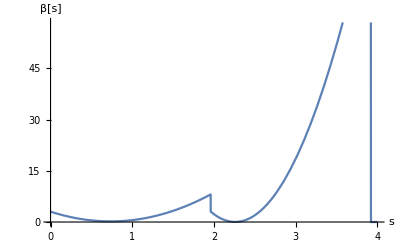

```mathematica
Plot[β[x]//.focus//.parastart//.para, {x, 0, 4}, AxesLabel-> {"s", "β[s]"}] (*keine Ahnung was ich dazu sagen soll oder was mir da auffällt, vielleicht habe ich auch i.wo einen Fehler gemacht, was nicht so unwahrscheinlich ist....*)
```

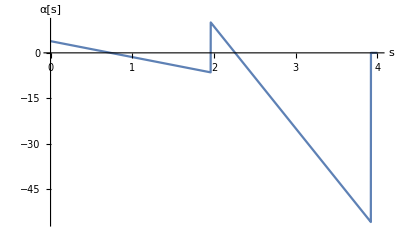

```mathematica
Plot[α[x]//.focus//.parastart//.para, {x, 0, 4}, AxesLabel-> {"s", "α[s]"}]
```

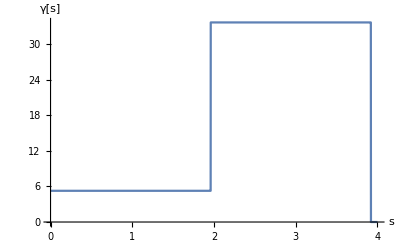

```mathematica
Plot[γ[x]//.focus//.parastart//.para, {x, 0, 4}, AxesLabel-> {"s", "γ[s]"}]
```

#### Die Funktion ℋ

Part::partw: Part 3 of (Piecewise[{{(cos(Times[«2»]) | ρ sin(«1») | ρ Plus[«2»]
-Power[«2»] sin(«1») | cos(Times[«2»]) | sin(Times[«2»])
0 | 0 | 1), 0.0000817143-L<L}, {(Times[«2»]+Times[«3»] | Times[«3»]+Times[«3»] | Times[«2»]+Times[«3»]+Times[«3»]
Times[«2»]+Times[«4»] | Times[«2»]+Times[«3»] | sin(«1»)+Times[«3»]+Times[«2»]
0 | 0 | 1), L<0.0000817143-L≤2 L}}]).{0,0,1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification {(L (1-cos(0.080898 Power[«2»] θ)))/θ,sin((0.080898 θ)/L),1}⟦3,2⟧ is longer than depth of object.

Part::partd: Part specification {0.00016428,0.0040614,1}⟦3,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

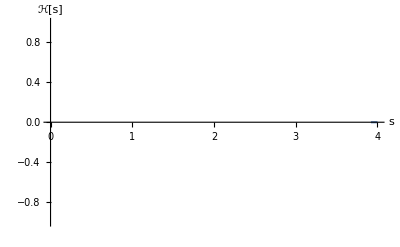

```mathematica
Plot[ℋ[x]//.focus//.parastart//.para, {x, 0, 4}, AxesLabel-> {"s", "ℋ[s]"}]
```

#### Richtige Optimierung

```mathematica
numH=ℋ[s]//.para//.focus//.γ0-> (1+α0^2)/β0;//FullSimplify
```

Part::partw: Part 3 of (Piecewise[{{(cos(Times[«2»]) | ρ sin(«1») | ρ Plus[«2»]
-Power[«2»] sin(«1») | cos(Times[«2»]) | sin(Times[«2»])
0 | 0 | 1), -L+s<L}, {(Times[«3»]+Times[«2»] | Times[«3»]+Times[«3»] | Times[«2»]+Times[«3»]+Times[«3»]
Times[«4»]+Times[«2»] | Times[«2»]+Times[«3»] | Times[«2»]+sin(«1»)+Times[«3»]
0 | 0 | 1), L<-L+s≤2 L}}]).{0,0,1} does not exist.

Part::partw: Part 3 of (Piecewise[{{(cos(Times[«3»]) | L Power[«2»] sin(«1») | L Power[«2»] Plus[«2»]
-Power[«2»] θ sin(«1») | cos(Times[«3»]) | sin(Times[«3»])
0 | 0 | 1), -1.96+s<1.96}, {(Times[«3»]+Times[«2»] | Times[«4»]+Times[«4»] | Times[«3»]+Times[«4»]+Times[«4»]
Times[«5»]+Times[«2»] | Times[«2»]+Times[«4»] | Times[«2»]+sin(«1»)+Times[«4»]
0 | 0 | 1), 1.96<-1.96+s≤3.92}}]).{0,0,1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
intH=Integrate[numH,{s,0,L}]//.para//FullSimplify (*Diese Integration sollte schon falsch sein, da diese nur über einen Dipol laufen würde. Wie du weiter unten siehst, liefert die Integration über beide Dipole leider kein Ergebnis. Ich weiß leider nicht wie ich das beheben kann. *)
```

Integrate::pwrl: Unable to prove that integration limits {0,L} are real. Adding assumptions may help.

Part::partw: Part 3 of (Piecewise[{{(cos(Times[«2»]) | 19.9187 sin(«1») | 19.9187 Plus[«2»]
-0.0502041 sin(«1») | cos(Times[«2»]) | sin(Times[«2»])
0 | 0 | 1), -1.96+s<1.96}, {(Times[«2»]+Times[«2»] | Times[«2»]+Times[«2»] | Times[«2»]+Times[«2»]+Times[«2»]
Times[«2»]+Times[«2»] | Times[«2»]+Times[«2»] | Times[«2»]+Times[«2»]+sin(«1»)
0 | 0 | 1), 1.96<-1.96+s≤3.92}}]).{0,0,1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

∫_0^1.96 (2 fullη(s) (Piecewise[{{α0-(s (α0^2+1))/β0, s≤1.96}, {-4.07834 (s-1.96) α0+α0-4.15821 (s-1.96) β0+2.03917 β0-((s-1.96) (α0^2+1))/β0, 1.96≤s≤3.92}}]) (Piecewise[{{(0.{0,0,1})⟦3,2⟧, s==3.92}, {{19.9187-19.9187 cos(0.0502041 (s-1.96)),sin(0.0502041 (s-1.96)),1}⟦3,2⟧, 1.96<s<3.92}}])+(Piecewise[{{((α0^2+1) s^2)/β0-2 α0 s+β0, s≤1.96}, {((α0^2+1) (s-1.96)^2)/β0-2. α0 (s-1.96)+4.07834 ((1. s-1.96) α0+(1.01958 s-2.99839) β0) (s-1.96)+β0, 1.96≤s≤3.92}}]) (Piecewise[{{(0.{0,0,1})⟦3,2⟧, s==3.92}, {{19.9187-19.9187 cos(0.0502041 (s-1.96)),sin(0.0502041 (s-1.96)),1}⟦3,2⟧, 1.96<s<3.92}}])^2+(fullη(s))^2 (Piecewise[{{(α0^2+1)/β0, s≤1.96}, {4.07834 α0+4.15821 β0+(α0^2+1.)/β0, 1.96≤s≤3.92}}]))ⅆs

```mathematica
nsβ=Solve[D[intH,β0]==0,β0]//FullSimplify (*da β0>0 sein soll, muss man die 2. Lösung nehmen*)
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[∂/(∂β0)(∫_0^1.96 (2 fullη(s) (Piecewise[{{α0-(s (α0^2+1))/β0, s≤1.96}, {-4.07834 (s-1.96) α0+α0-4.15821 (s-1.96) β0+2.03917 β0-((s-1.96) (α0^2+1))/β0, 1.96≤s≤3.92}}]) (Piecewise[{{(0.{0,0,1})⟦3,2⟧, s==3.92}, {{19.9187-19.9187 cos(0.0502041 (s-1.96)),sin(0.0502041 (s-1.96)),1}⟦3,2⟧, 1.96<s<3.92}}])+(Piecewise[{{((α0^2+1) s^2)/β0-2 α0 s+β0, s≤1.96}, {((α0^2+1) (s-1.96)^2)/β0-2. α0 (s-1.96)+4.07834 ((1. s-1.96) α0+(1.01958 s-2.99839) β0) (s-1.96)+β0, 1.96≤s≤3.92}}]) (Piecewise[{{(0.{0,0,1})⟦3,2⟧, s==3.92}, {{19.9187-19.9187 cos(0.0502041 (s-1.96)),sin(0.0502041 (s-1.96)),1}⟦3,2⟧, 1.96<s<3.92}}])^2+(fullη(s))^2 (Piecewise[{{(α0^2+1)/β0, s≤1.96}, {4.07834 α0+4.15821 β0+(α0^2+1.)/β0, 1.96≤s≤3.92}}]))ⅆs)==0,β0]

```mathematica
nsα=Solve[D[intH,α0]==0,α0]//FullSimplify//Flatten
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[∂/(∂α0)(∫_0^1.96 (2 fullη(s) (Piecewise[{{α0-(s (α0^2+1))/β0, s≤1.96}, {-4.07834 (s-1.96) α0+α0-4.15821 (s-1.96) β0+2.03917 β0-((s-1.96) (α0^2+1))/β0, 1.96≤s≤3.92}}]) (Piecewise[{{(0.{0,0,1})⟦3,2⟧, s==3.92}, {{19.9187-19.9187 cos(0.0502041 (s-1.96)),sin(0.0502041 (s-1.96)),1}⟦3,2⟧, 1.96<s<3.92}}])+(Piecewise[{{((α0^2+1) s^2)/β0-2 α0 s+β0, s≤1.96}, {((α0^2+1) (s-1.96)^2)/β0-2. α0 (s-1.96)+4.07834 ((1. s-1.96) α0+(1.01958 s-2.99839) β0) (s-1.96)+β0, 1.96≤s≤3.92}}]) (Piecewise[{{(0.{0,0,1})⟦3,2⟧, s==3.92}, {{19.9187-19.9187 cos(0.0502041 (s-1.96)),sin(0.0502041 (s-1.96)),1}⟦3,2⟧, 1.96<s<3.92}}])^2+(fullη(s))^2 (Piecewise[{{(α0^2+1)/β0, s≤1.96}, {4.07834 α0+4.15821 β0+(α0^2+1.)/β0, 1.96≤s≤3.92}}]))ⅆs)==0,α0]

```mathematica
test=Integrate[numH//.ρ-> L/θ,{s,0,2*L}]//.para//FullSimplify
```

Part::partw: Part 3 of (Piecewise[{{(cos(Times[«2»]) | 19.9187 sin(«1») | 19.9187 Plus[«2»]
-0.0502041 sin(«1») | cos(Times[«2»]) | sin(Times[«2»])
0 | 0 | 1), -1.96+s<1.96}, {(Times[«2»]+Times[«2»] | Times[«2»]+Times[«2»] | Times[«2»]+Times[«2»]+Times[«2»]
Times[«2»]+Times[«2»] | Times[«2»]+Times[«2»] | Times[«2»]+Times[«2»]+sin(«1»)
0 | 0 | 1), 1.96<-1.96+s≤3.92}}]).{0,0,1} does not exist.

Integrate::pwrl: Unable to prove that integration limits {0,2 L} are real. Adding assumptions may help.

Part::partw: Part 3 of (Piecewise[{{(cos(Times[«2»]) | 19.9187 sin(«1») | 19.9187 Plus[«2»]
-0.0502041 sin(«1») | cos(Times[«2»]) | sin(Times[«2»])
0 | 0 | 1), -1.96+s<1.96}, {(Times[«2»]+Times[«2»] | Times[«2»]+Times[«2»] | Times[«2»]+Times[«2»]+Times[«2»]
Times[«2»]+Times[«2»] | Times[«2»]+Times[«2»] | Times[«2»]+Times[«2»]+sin(«1»)
0 | 0 | 1), 1.96<-1.96+s≤3.92}}]).{0,0,1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

∫_0^3.92 (2 fullη(s) (Piecewise[{{α0-(s (α0^2+1))/β0, s≤1.96}, {-4.07834 (s-1.96) α0+α0-4.15821 (s-1.96) β0+2.03917 β0-((s-1.96) (α0^2+1))/β0, 1.96≤s≤3.92}}]) (Piecewise[{{(0.{0,0,1})⟦3,2⟧, s==3.92}, {{19.9187-19.9187 cos(0.0502041 (s-1.96)),sin(0.0502041 (s-1.96)),1}⟦3,2⟧, 1.96<s<3.92}}])+(Piecewise[{{((α0^2+1) s^2)/β0-2 α0 s+β0, s≤1.96}, {((α0^2+1) (s-1.96)^2)/β0-2. α0 (s-1.96)+4.07834 ((1. s-1.96) α0+(1.01958 s-2.99839) β0) (s-1.96)+β0, 1.96≤s≤3.92}}]) (Piecewise[{{(0.{0,0,1})⟦3,2⟧, s==3.92}, {{19.9187-19.9187 cos(0.0502041 (s-1.96)),sin(0.0502041 (s-1.96)),1}⟦3,2⟧, 1.96<s<3.92}}])^2+(fullη(s))^2 (Piecewise[{{(α0^2+1)/β0, s≤1.96}, {4.07834 α0+4.15821 β0+(α0^2+1.)/β0, 1.96≤s≤3.92}}]))ⅆs